```mathematica
Kd1Equation = Kd1 == CrpFree*C1Free/CrpC1
```

Kd1==(C1Free CrpFree)/CrpC1

```mathematica
Kd2Equation=Kd2==CrpFree*C2Free/CrpC2
```

Kd2==(C2Free CrpFree)/CrpC2

```mathematica
SolCrpC1 = Flatten@@Solve[C1Total == C1Free+ CrpC1, CrpC1]
SolCrpC2 = Flatten@@Solve[C2Total == C2Free+ CrpC2, CrpC2]
```

{CrpC1→-C1Free+C1Total}

{CrpC2→-C2Free+C2Total}

```mathematica
SolCrpFree = Flatten[Solve[(CrpTotal==CrpFree+CrpC1+CrpC2)/.Join[SolCrpC1, SolCrpC2], CrpFree]]
```

{CrpFree→C1Free-C1Total+C2Free-C2Total+CrpTotal}

```mathematica
Kd1Solved = Kd1Equation/.SolCrpFree/.SolCrpC1
```

Kd1==(C1Free (C1Free-C1Total+C2Free-C2Total+CrpTotal))/(-C1Free+C1Total)

```mathematica
Kd2Solved = Kd2Equation/.SolCrpFree/.SolCrpC2
```

Kd2==(C2Free (C1Free-C1Total+C2Free-C2Total+CrpTotal))/(-C2Free+C2Total)

```mathematica
(* now we want to create an "activity" level for each promoter, i.e. C1Free/C1Total *)
```

```mathematica
v1=k1f*((CrpC1/.SolCrpC1)-C1Free*(CrpTotal-(CrpC1/.SolCrpC1)-(CrpC2/.SolCrpC2))/Kd1)
```

k1f (-C1Free+C1Total-(C1Free (C1Free-C1Total+C2Free-C2Total+CrpTotal))/Kd1)

```mathematica
v2=k2f*((CrpC2/.SolCrpC2)-C2Free*(CrpTotal-(CrpC1/.SolCrpC1)-(CrpC2/.SolCrpC2))/Kd2)
```

k2f (-C2Free+C2Total-(C2Free (C1Free-C1Total+C2Free-C2Total+CrpTotal))/Kd2)

```mathematica
(* set up values *)
kVals={k1f->1, k2f->1}
KdVals={Kd1->10, Kd2->250}
CrpTotalVal={CrpTotal->10}
CTotalVals={C1Total->100, C2Total->100}
v1t=k1f(-C1Free[t]+C1Total-C1Free[t](CrpTotal+C1Free[t]-C1Total+C2Free[t]-C2Total)/Kd1)
v2t=k2f(-C2Free[t]+C2Total-C2Free[t](CrpTotal+C1Free[t]-C1Total+C2Free[t]-C2Total)/Kd2)
```

{k1f→1,k2f→1}

{Kd1→10,Kd2→250}

{CrpTotal→10}

{C1Total→100,C2Total→100}

k1f (C1Total-C1Free[t]-(C1Free[t] (-C1Total-C2Total+CrpTotal+C1Free[t]+C2Free[t]))/Kd1)

k2f (C2Total-C2Free[t]-(C2Free[t] (-C1Total-C2Total+CrpTotal+C1Free[t]+C2Free[t]))/Kd2)

```mathematica
MBst = {C1Free'[t]== v1t,
C2Free'[t] == v2t}
```

{C1Free'[t]==k1f (C1Total-C1Free[t]-(C1Free[t] (-C1Total-C2Total+CrpTotal+C1Free[t]+C2Free[t]))/Kd1),C2Free'[t]==k2f (C2Total-C2Free[t]-(C2Free[t] (-C1Total-C2Total+CrpTotal+C1Free[t]+C2Free[t]))/Kd2)}

```mathematica
concInit = {C1Free[0]== 1,  C2Free[0]==1}
```

{C1Free[0]==1,C2Free[0]==1}

```mathematica
tEnd = 10000
sol = NDSolve[Flatten[Join[MBst/.kVals/.KdVals/.CTotalVals/.CrpTotalVal,concInit]],{C1Free,C2Free}, {t,10000}]
```

10000

{{C1Free→InterpolatingFunction[…],C2Free→InterpolatingFunction[…]}}

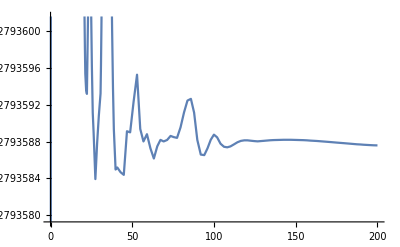

```mathematica
Plot[C1Free[t]/.sol,{t,0,200}]
```

```mathematica
C1ValFinal=(C1Free[tEnd]/.sol)/(C1Total/.CTotalVals)
C2ValFinal=(C2Free[tEnd]/.sol)/(C2Total/.CTotalVals)
```

{0.913279}

{0.996216}

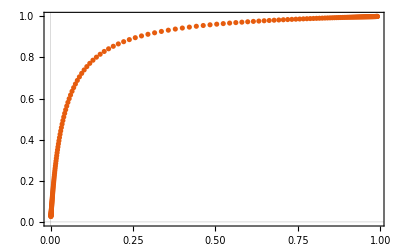

```mathematica
(* note, this shows fraction unbound *)
CrpList =PowerRange[1, 10000, 1.05];
listC1Final = {};
listC2Final = {};
Do[
CrpTotalVal = {CrpTotal-> CrpVal};
tEnd = 10000;
sol = NDSolve[Flatten[Join[MBst/.kVals/.KdVals/.CTotalVals/.CrpTotalVal,concInit]],{C1Free,C2Free},{t,10000}];
C1ValFinal=(C1Free[tEnd]/.sol)/(C1Total/.CTotalVals);
C2ValFinal=(C2Free[tEnd]/.sol)/(C2Total/.CTotalVals);
listC1Final = Flatten[Append[listC1Final,C1ValFinal]];
listC2Final = Flatten[Append[listC2Final,C2ValFinal]];
,{CrpVal,CrpList}]
data=Transpose@{listC1Final,listC2Final};
ListPlot[data, PlotTheme->"Scientific"]
```

```mathematica
data
```

{{0.991237,0.999647},{0.9908,0.999629},{0.99034,0.99961},{0.989858,0.99959},{0.989352,0.99957},{0.98882,0.999548},{0.988262,0.999525},{0.987676,0.999501},{0.98706,0.999476},{0.986415,0.999449},{0.985737,0.999422},{0.985025,0.999392},{0.984277,0.999361},{0.983493,0.999329},{0.982669,0.999295},{0.981805,0.999259},{0.980897,0.999222},{0.979944,0.999182},{0.978944,0.99914},{0.977894,0.999097},{0.976792,0.999051},{0.975636,0.999002},{0.974421,0.998951},{0.973147,0.998897},{0.971809,0.998841},{0.970405,0.998782},{0.968931,0.998719},{0.967384,0.998653},{0.96576,0.998584},{0.964056,0.998511},{0.962268,0.998434},{0.960391,0.998353},{0.958421,0.998268},{0.956354,0.998178},{0.954185,0.998083},{0.951909,0.997983},{0.94952,0.997878},{0.947014,0.997767},{0.944384,0.99765},{0.941625,0.997526},{0.938731,0.997396},{0.935694,0.997259},{0.932508,0.997113},{0.929167,0.99696},{0.925661,0.996798},{0.921985,0.996627},{0.918129,0.996446},{0.914085,0.996254},{0.909844,0.996052},{0.905397,0.995838},{0.900735,0.995611},{0.895847,0.995371},{0.890724,0.995117},{0.885353,0.994847},{0.879724,0.994561},{0.873826,0.994257},{0.867645,0.993935},{0.86117,0.993593},{0.854388,0.993229},{0.847285,0.992842},{0.839847,0.99243},{0.832061,0.991991},{0.823911,0.991524},{0.815382,0.991025},{0.80646,0.990492},{0.797129,0.989922},{0.787372,0.989314},{0.777175,0.988662},{0.76652,0.987963},{0.755393,0.987213},{0.743777,0.986408},{0.731657,0.985542},{0.719018,0.984609},{0.705846,0.983604},{0.692128,0.982518},{0.677853,0.981345},{0.66301,0.980074},{0.647592,0.978696},{0.631593,0.9772},{0.615012,0.975572},{0.597852,0.973799},{0.58012,0.971863},{0.561828,0.969748},{0.542996,0.967431},{0.523653,0.964891},{0.503833,0.962102},{0.483584,0.959034},{0.462963,0.955658},{0.442039,0.951937},{0.420894,0.947835},{0.399621,0.943312},{0.378327,0.938325},{0.357128,0.932832},{0.336147,0.926788},{0.315512,0.920151},{0.295351,0.912882},{0.275788,0.904945},{0.256934,0.896313},{0.238888,0.886963},{0.221727,0.876884},{0.20551,0.866072},{0.19027,0.854535},{0.176022,0.842287},{0.16276,0.829352},{0.15046,0.81576},{0.139089,0.801548},{0.128601,0.786757},{0.118944,0.771431},{0.110065,0.755617},{0.101907,0.739364},{0.0944151,0.72272},{0.0875357,0.705738},{0.0812177,0.688467},{0.0754135,0.670957},{0.0700785,0.653258},{0.0651717,0.63542},{0.0606556,0.617489},{0.0564958,0.599514},{0.0526611,0.581539},{0.0491231,0.563609},{0.045856,0.545763},{0.0428365,0.528044},{0.0400435,0.510487},{0.0374577,0.493128},{0.0350618,0.475999},{0.03284,0.459131},{0.0307779,0.44255},{0.0288627,0.42628},{0.0270823,0.410344},{0.0254262,0.39476},{0.0238844,0.379545},{0.022448,0.364711},{0.0211089,0.350271},{0.0198596,0.336232},{0.0186933,0.322601},{0.0176037,0.309382},{0.0165852,0.296578},{0.0156325,0.284189},{0.0147407,0.272214},{0.0139055,0.26065},{0.0131229,0.249494},{0.012389,0.238739},{0.0117005,0.22838},{0.0110541,0.21841},{0.0104471,0.20882},{0.00987666,0.199603},{0.00934033,0.190749},{0.00883583,0.182248},{0.00836103,0.174092},{0.00791398,0.166269},{0.00749286,0.15877},{0.007096,0.151585},{0.00672184,0.144702},{0.00636894,0.138112},{0.00603595,0.131805},{0.00572163,0.12577},{0.00542483,0.119998},{0.00514446,0.114477},{0.00487953,0.1092},{0.0046291,0.104156},{0.0043923,0.0993361},{0.00416833,0.0947313},{0.00395642,0.0903329},{0.00375586,0.0861325},{0.003566,0.0821217},{0.00338622,0.0782927},{0.00321594,0.0746378},{0.00305462,0.0711494},{0.00290175,0.0678205},{0.00275685,0.0646442},{0.00261949,0.0616137},{0.00248924,0.0587228},{0.00236571,0.0559652},{0.00224853,0.0533351},{0.00213736,0.0508267},{0.00203186,0.0484347},{0.00193174,0.0461537},{0.0018367,0.0439789},{0.00174647,0.0419053},{0.0016608,0.0399285},{0.00157944,0.0380439},{0.00150217,0.0362475},{0.00142877,0.0345351},{0.00135904,0.0329029},{0.00129279,0.0313472},{0.00122984,0.0298645},{0.00117002,0.0284515},{0.00111316,0.0271048},{0.00105912,0.0258215}}

```mathematica
Export["crp_binding.csv",data]
```

crp_binding.csv